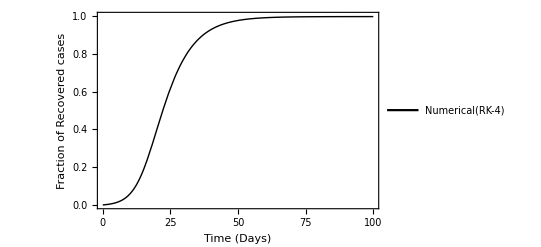

```mathematica
beta=0.75; gamma=1/8; sigma=1/3;I0=0.01; S0=0.98; E0=0.01; R0=0;
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
P0=Plot[{R1[t]/.Sol1},{t,0,100},PlotRange->{0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Recovered cases",Bold,Black]},PlotLegends->Placed[{Style["Numerical(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]]
```

```mathematica
f[i_,j_]:=(j)^(i-1);
```

```mathematica
n=5;
Mn=Table[f[i,j],{i,n},{j,n}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,n-1}];
Soln=Inverse[Mn].Nn;
R5[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,n}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

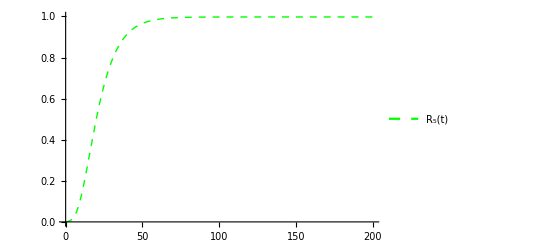

```mathematica
PR5=Plot[R5[x],{x,0,200},PlotRange->{0,1},PlotStyle->{Green,Thick,Dashed},PlotLegends->Placed[{Style["R_5(t)",Bold,Black]},{Right,Top}]]
```

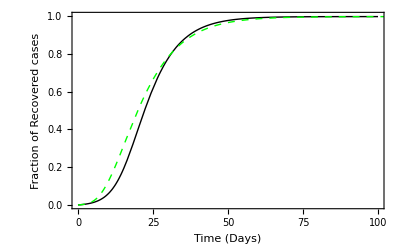

```mathematica
Show[P0,PR5]
```

```mathematica
n=10;
Mn=Table[f[i,j],{i,n},{j,n}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,n-1}];
Soln=Inverse[Mn].Nn;
R10[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,n}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

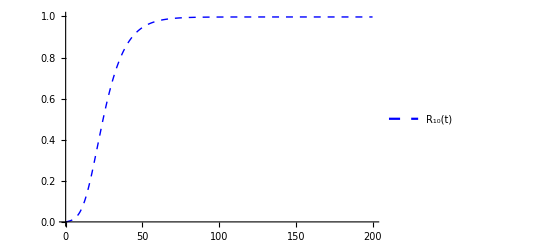

```mathematica
PR10=Plot[R10[x],{x,0,200},PlotRange->{0,1},PlotStyle->{Blue,Thick,Dashed},PlotLegends->Placed[{Style["R_10(t)",Bold,Black]},{Right,Top}]]
```

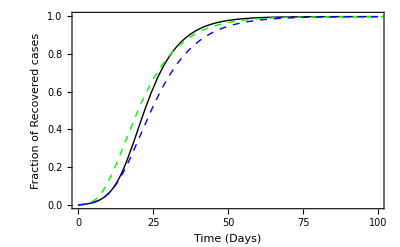

```mathematica
Show[P0,PR5,PR10]
```

```mathematica
n=15;
Mn=Table[f[i,j],{i,n},{j,n}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,n-1}];
Soln=Inverse[Mn].Nn;
R15[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,n}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
R10[x]
```

0.997535+0.386632 ⅇ^(-1.5 x)-5.64352 ⅇ^(-1.4 x)+38.2529 ⅇ^(-1.3 x)-159.486 ⅇ^(-1.2 x)+456.443 ⅇ^(-1.1 x)-946.867 ⅇ^(-1. x)+1463.53 ⅇ^(-0.9 x)-1702.06 ⅇ^(-0.8 x)+1478.86 ⅇ^(-0.7 x)-929.503 ⅇ^(-0.6 x)+384.541 ⅇ^(-0.5 x)-68.2183 ⅇ^(-0.4 x)-27.5659 ⅇ^(-0.3 x)+23.8107 ⅇ^(-0.2 x)-7.47452 ⅇ^(-0.1 x)

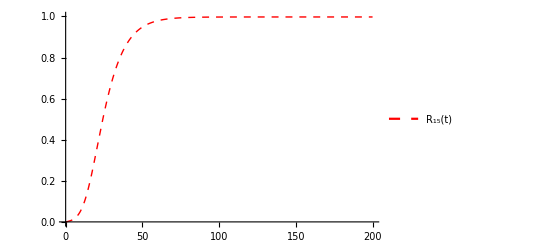

```mathematica
PR15=Plot[R15[x],{x,0,200},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed},PlotLegends->Placed[{Style["R_15(t)",Bold,Black]},{Right,Top}]]
```

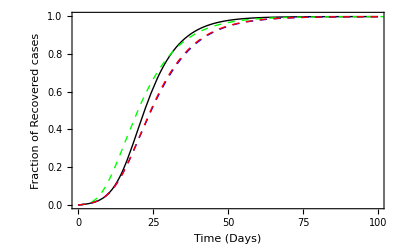

```mathematica
Show[P0,PR5,PR10,PR15]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

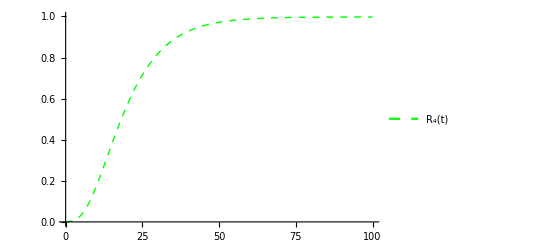

```mathematica
Mn=Table[f[i,j],{i,4},{j,4}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,4-1}];
Soln=Inverse[Mn].Nn;
R4[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,4}];
PR4=Plot[R4[x],{x,0,100},PlotRange->{0,1},PlotStyle->{Green,Thick,Dashed},PlotLegends->Placed[{Style["R_4(t)",Bold,Black]},{Right,Top}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

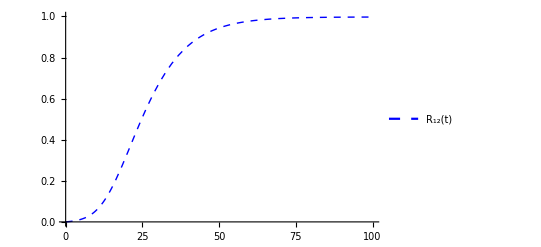

```mathematica
Mn=Table[f[i,j],{i,12},{j,12}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,12-1}];
Soln=Inverse[Mn].Nn;
R12[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,12}];
PR12=Plot[R12[x],{x,0,100},PlotRange->{0,1},PlotStyle->{Blue,Thick,Dashed},PlotLegends->Placed[{Style["R_12(t)",Bold,Black]},{Right,Top}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

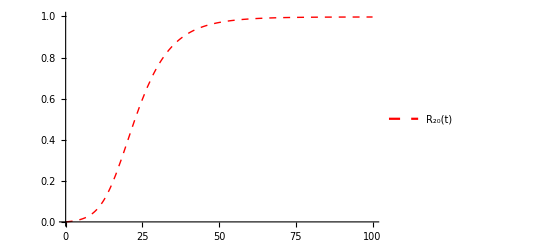

```mathematica
Mn=Table[f[i,j],{i,20},{j,20}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,20-1}];
Soln=Inverse[Mn].Nn;
R20[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,20}];
PR20=Plot[R20[x],{x,0,100},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed},PlotLegends->Placed[{Style["R_20(t)",Bold,Black]},{Right,Top}]]
```

```mathematica
R20[t]
```

0.997535-0.906981 ⅇ^(-2. t)+18.0889 ⅇ^(-1.9 t)-171.28 ⅇ^(-1.8 t)+1023.69 ⅇ^(-1.7 t)-4330.52 ⅇ^(-1.6 t)+13780.6 ⅇ^(-1.5 t)-34219. ⅇ^(-1.4 t)+67872.2 ⅇ^(-1.3 t)-109161. ⅇ^(-1.2 t)+143670. ⅇ^(-1.1 t)-155430. ⅇ^(-1. t)+138262. ⅇ^(-0.9 t)-100721. ⅇ^(-0.8 t)+59540.1 ⅇ^(-0.7 t)-28099.4 ⅇ^(-0.6 t)+10297. ⅇ^(-0.5 t)-2786.09 ⅇ^(-0.4 t)+499.369 ⅇ^(-0.3 t)-40.602 ⅇ^(-0.2 t)-3.74085 ⅇ^(-0.1 t)

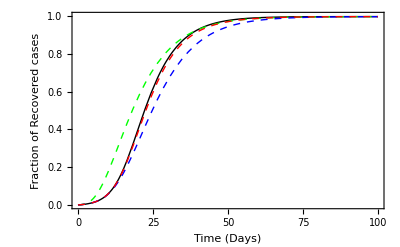

```mathematica
Show[P0,PR4,PR12,PR20]
```

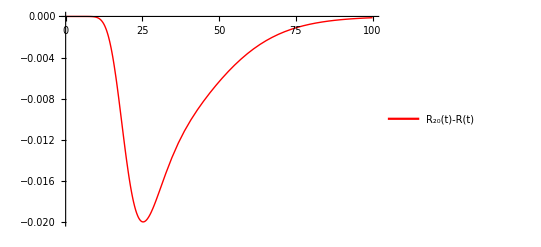

```mathematica
Plot[R20[x]-R1[x]/.Sol1,{x,0,100},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["R_20(t)-R(t)",Bold,Black]},{Right,Bottom}]]
```

```mathematica
Sum[(R20[x]-R1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000675307}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

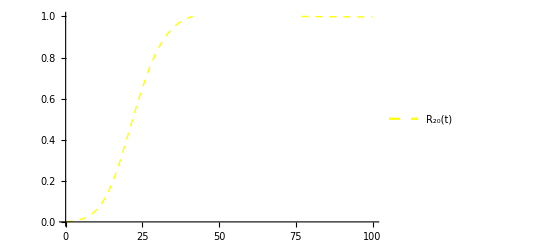

```mathematica
Mn=Table[f[i,j],{i,20},{j,20}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.09;
Nn=Table[F[n],{n,0,20-1}];
Soln=Inverse[Mn].Nn;
R20[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,20}];
PR20=Plot[R20[x],{x,0,100},PlotRange->{0,1},PlotStyle->{Yellow,Thick,Dashed},PlotLegends->Placed[{Style["R_20(t)",Bold,Black]},{Right,Top}]]
```

```mathematica
R15[x]
```

0.997535+0.386632 ⅇ^(-1.5 x)-5.64352 ⅇ^(-1.4 x)+38.2529 ⅇ^(-1.3 x)-159.486 ⅇ^(-1.2 x)+456.443 ⅇ^(-1.1 x)-946.867 ⅇ^(-1. x)+1463.53 ⅇ^(-0.9 x)-1702.06 ⅇ^(-0.8 x)+1478.86 ⅇ^(-0.7 x)-929.503 ⅇ^(-0.6 x)+384.541 ⅇ^(-0.5 x)-68.2183 ⅇ^(-0.4 x)-27.5659 ⅇ^(-0.3 x)+23.8107 ⅇ^(-0.2 x)-7.47452 ⅇ^(-0.1 x)

```mathematica
R10[x]
```

0.997535-946.867 ⅇ^(-1. x)+1463.53 ⅇ^(-0.9 x)-1702.06 ⅇ^(-0.8 x)+1478.86 ⅇ^(-0.7 x)-929.503 ⅇ^(-0.6 x)+384.541 ⅇ^(-0.5 x)-68.2183 ⅇ^(-0.4 x)-27.5659 ⅇ^(-0.3 x)+23.8107 ⅇ^(-0.2 x)-7.47452 ⅇ^(-0.1 x)

```mathematica
R5[x]
```

0.997535+384.541 ⅇ^(-0.5 x)-68.2183 ⅇ^(-0.4 x)-27.5659 ⅇ^(-0.3 x)+23.8107 ⅇ^(-0.2 x)-7.47452 ⅇ^(-0.1 x)

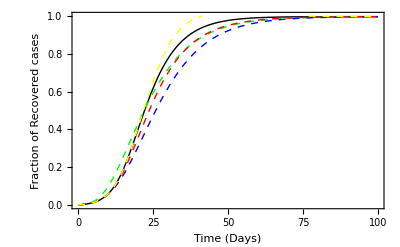

```mathematica
Show[P0,PR5,PR10,PR15,PR20]
```

```mathematica
I4=(1/gamma)*D[R4[x],x]
```

8 (1114.44 ⅇ^(-0.4 x)-149.811 ⅇ^(-0.3 x)+8.12041 ⅇ^(-0.2 x)+0.374085 ⅇ^(-0.1 x))

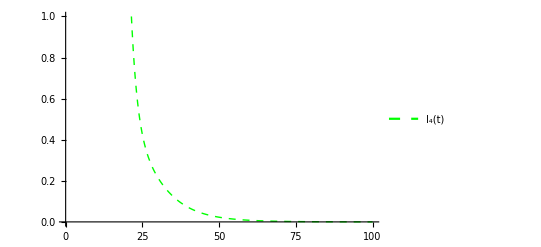

```mathematica
PI4=Plot[I4,{x,0,100},PlotRange->{0,1},PlotStyle->{Green,Thick,Dashed},PlotLegends->Placed[{Style["I_4(t)",Bold,Black]},{Right,Top}]]
```

8 (130993. ⅇ^(-1.2 x)-158037. ⅇ^(-1.1 x)+155430. ⅇ^(-1. x)-124436. ⅇ^(-0.9 x)+80576.9 ⅇ^(-0.8 x)-41678.1 ⅇ^(-0.7 x)+16859.7 ⅇ^(-0.6 x)-5148.5 ⅇ^(-0.5 x)+1114.44 ⅇ^(-0.4 x)-149.811 ⅇ^(-0.3 x)+8.12041 ⅇ^(-0.2 x)+0.374085 ⅇ^(-0.1 x))

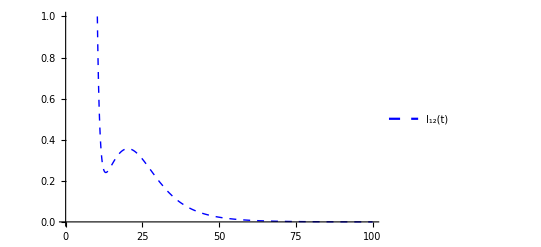

```mathematica
I12=(1/gamma)*D[R12[x],x]
PI12=Plot[I12,{x,0,100},PlotRange->{0,1},PlotStyle->{Blue,Thick,Dashed},PlotLegends->Placed[{Style["I_12(t)",Bold,Black]},{Right,Top}]]
```

8 (1.81396 ⅇ^(-2. x)-34.3689 ⅇ^(-1.9 x)+308.304 ⅇ^(-1.8 x)-1740.27 ⅇ^(-1.7 x)+6928.83 ⅇ^(-1.6 x)-20670.9 ⅇ^(-1.5 x)+47906.6 ⅇ^(-1.4 x)-88233.9 ⅇ^(-1.3 x)+130993. ⅇ^(-1.2 x)-158037. ⅇ^(-1.1 x)+155430. ⅇ^(-1. x)-124436. ⅇ^(-0.9 x)+80576.9 ⅇ^(-0.8 x)-41678.1 ⅇ^(-0.7 x)+16859.7 ⅇ^(-0.6 x)-5148.5 ⅇ^(-0.5 x)+1114.44 ⅇ^(-0.4 x)-149.811 ⅇ^(-0.3 x)+8.12041 ⅇ^(-0.2 x)+0.374085 ⅇ^(-0.1 x))

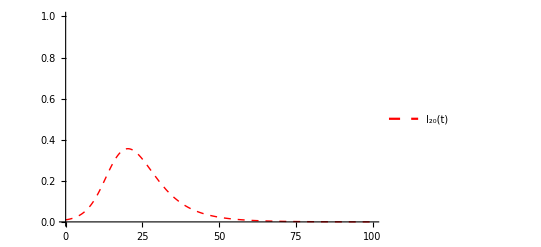

```mathematica
I20=(1/gamma)*D[R20[x],x]
PI20=Plot[I20,{x,0,100},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed},PlotLegends->Placed[{Style["I_20(t)",Bold,Black]},{Right,Top}]]
```

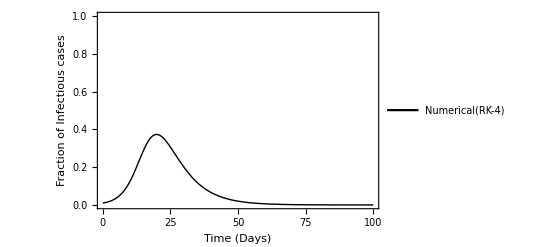

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PI0=Plot[{I1[t]/.Sol1},{t,0,100},PlotRange->{0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Infectious cases",Bold,Black]},PlotLegends->Placed[{Style["Numerical(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]]
```

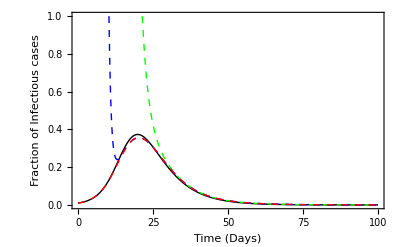

```mathematica
Show[PI0,PI4,PI12,PI20]
```

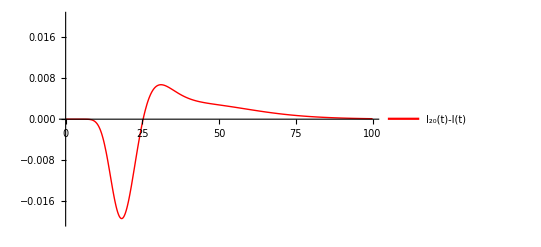

```mathematica
Plot[I20-I1[x]/.Sol1,{x,0,100},PlotRange->{-0.02,0.02},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["I_20(t)-I(t)",Bold,Black]},{Right,Bottom}]]
```

```mathematica
Sum[(I20-I1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000287791}

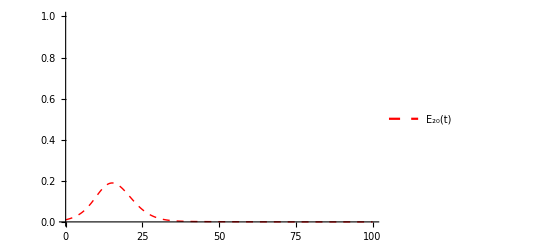

```mathematica
E20=(1/sigma)*(gamma*I20 +D[I20,x]);
PE20=Plot[E20,{x,0,100},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed},PlotLegends->Placed[{Style["E_20(t)",Bold,Black]},{Right,Top}]]
```

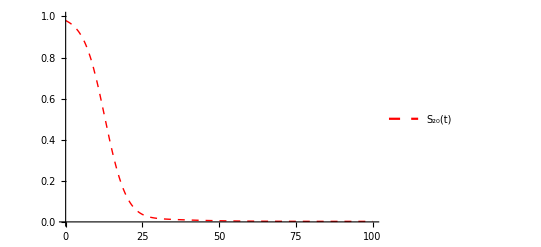

```mathematica
S20=1-E20-I20-R20[x];
PS20=Plot[S20,{x,0,100},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed},PlotLegends->Placed[{Style["S_20(t)",Bold,Black]},{Right,Top}]]
```

```mathematica
Mn=Table[f[i,j],{i,12},{j,12}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,12-1}];
Soln=Inverse[Mn].Nn;
R12[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,12}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

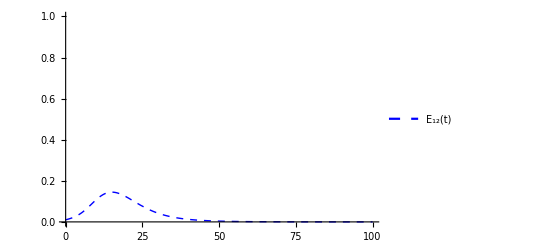

```mathematica
E12=(1/sigma)*(gamma*I12 +D[I12,x]);
PE12=Plot[E12,{x,0,100},PlotRange->{0,1},PlotStyle->{Blue,Thick,Dashed},PlotLegends->Placed[{Style["E_12(t)",Bold,Black]},{Right,Top}]]
```

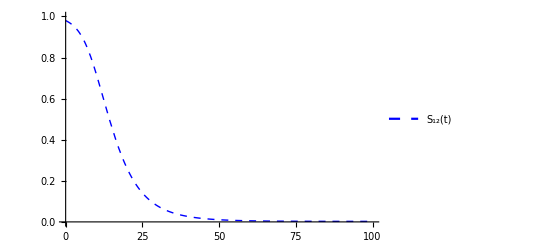

```mathematica
S12=1-E12-I12-R12[x];
PS12=Plot[S12,{x,0,100},PlotRange->{0,1},PlotStyle->{Blue,Thick,Dashed},PlotLegends->Placed[{Style["S_12(t)",Bold,Black]},{Right,Top}]]
```

```mathematica
Mn=Table[f[i,j],{i,4},{j,4}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,4-1}];
Soln=Inverse[Mn].Nn;
R4[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,4}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

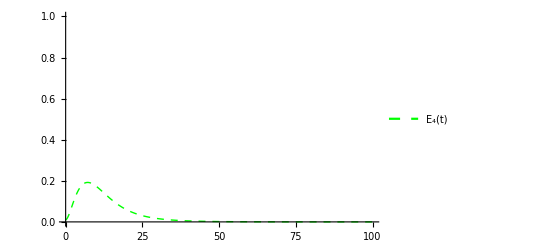

```mathematica
E4=(1/sigma)*(gamma*I4 +D[I4,x]);
PE4=Plot[E4,{x,0,100},PlotRange->{0,1},PlotStyle->{Green,Thick,Dashed},PlotLegends->Placed[{Style["E_4(t)",Bold,Black]},{Right,Top}]]
```

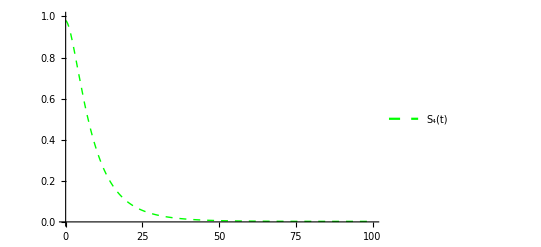

```mathematica
S4=1-E4-I4-R4[x];
PS4=Plot[S4,{x,0,100},PlotRange->{0,1},PlotStyle->{Green,Thick,Dashed},PlotLegends->Placed[{Style["S_4(t)",Bold,Black]},{Right,Top}]]
```

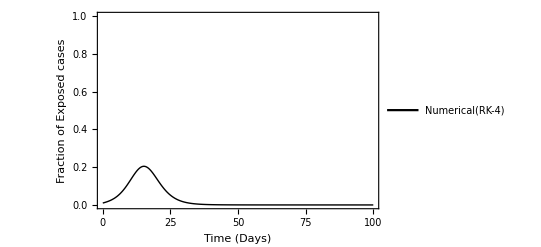

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PE0=Plot[{E1[t]/.Sol1},{t,0,100},PlotRange->{0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Exposed cases",Bold,Black]},PlotLegends->Placed[{Style["Numerical(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]]
```

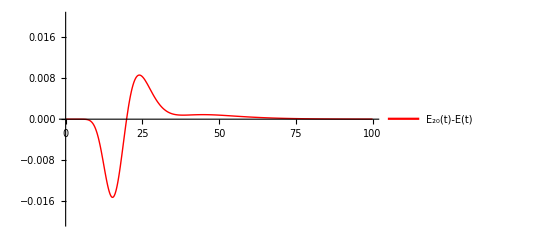

```mathematica
Plot[E20-E1[x]/.Sol1,{x,0,100},PlotStyle->{Red,Thick},PlotRange->{-0.02,0.02},PlotLegends->Placed[{Style["E_20(t)-E(t)",Bold,Black]},{Right,Bottom}]]
```

```mathematica
Sum[(E20-E1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000150904}

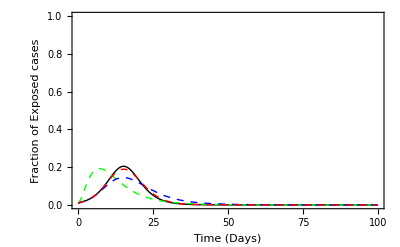

```mathematica
Show[PE0,PE4,PE12,PE20]
```

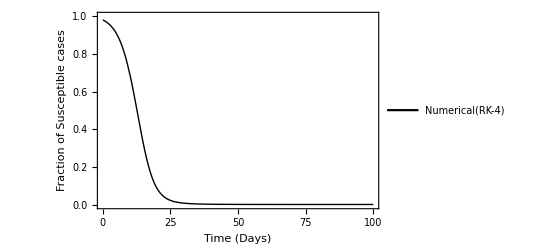

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PS0=Plot[{S1[t]/.Sol1},{t,0,100},PlotRange->{0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Susceptible cases",Bold,Black]},PlotLegends->Placed[{Style["Numerical(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]]
```

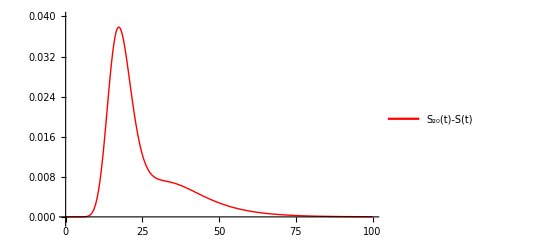

```mathematica
Plot[S20-S1[x]/.Sol1,{x,0,100},PlotStyle->{Red,Thick},PlotRange->{-0.001,0.04},PlotLegends->Placed[{Style["S_20(t)-S(t)",Bold,Black]},{Right,Top}]]
```

```mathematica
Sum[(S20-S1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.000111401}

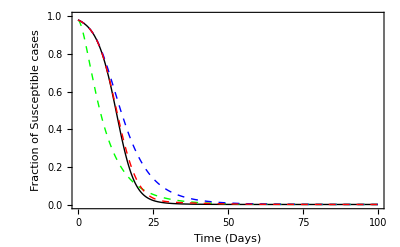

```mathematica
Show[PS0,PS4,PS12,PS20]
```

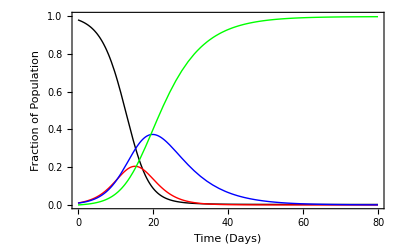

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,80}];
PSS0=Plot[{S1[t]/.Sol1},{t,0,80},PlotRange->{0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Population",Bold,Black]},PlotLegends->Placed[{Style["Susceptible(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]];
PEE0=Plot[{E1[t]/.Sol1},{t,0,80},PlotRange->{0,1},PlotStyle->{Red,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Population",Bold,Black]},PlotLegends->Placed[{Style["Exposed(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]];
PII0=Plot[{I1[t]/.Sol1},{t,0,80},PlotRange->{0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Population",Bold,Black]},PlotLegends->Placed[{Style["Infectious(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]];
PRR0=Plot[{R1[t]/.Sol1},{t,0,80},PlotRange->{0,1},PlotStyle->{Green,Thick},FrameLabel->{Style["Time (Days)",Bold,Black], Style["Fraction of Population",Bold,Black]},PlotLegends->Placed[{Style["Recovered(RK-4)",Bold,Black]},{Right,Top}],Frame-> True,FrameTicksStyle->Directive[Black,12]];
Show[PSS0,PEE0,PII0,PRR0]
```

```mathematica
Mn=Table[f[i,j],{i,20},{j,20}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,20-1}];
Soln=Inverse[Mn].Nn;
R20[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,20}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
PR20=Plot[R20[x],{x,0,100},PlotRange->{0,1},PlotStyle->{Black,Thick,Dashed},PlotLegends->Placed[{Style["R_20(t)",Bold,Black]},{Right,Top}]];
I20=(1/gamma)*D[R20[x],x];
PI20=Plot[I20,{x,0,100},PlotRange->{0,1},PlotStyle->{Orange,Thick,Dashed},PlotLegends->Placed[{Style["I_20(t)",Bold,Black]},{Right,Top}]];
E20=(1/sigma)*(gamma*I20 +D[I20,x]);
PE20=Plot[E20,{x,0,100},PlotRange->{0,1},PlotStyle->{Brown,Thick,Dashed},PlotLegends->Placed[{Style["E_20(t)",Bold,Black]},{Right,Top}]];
S20=1-E20-I20-R20[x];
PS20=Plot[S20,{x,0,100},PlotRange->{0,1},PlotStyle->{Yellow,Thick,Dashed},PlotLegends->Placed[{Style["S_20(t)",Bold,Black]},{Right,Top}]];
```

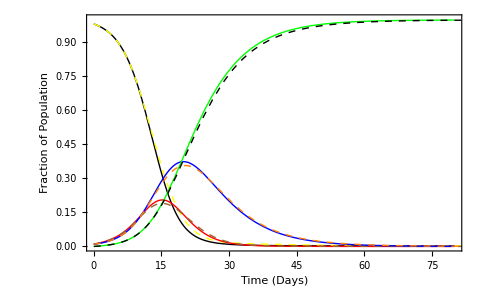

```mathematica
Show[PSS0,PS20,PEE0,PE20,PII0,PI20,PRR0,PR20]
```